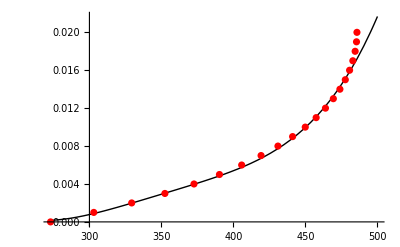

```mathematica
Module[{Ta,t,L,u,Cp,ka,ν,ρ,μ,Pr,Rex,h,P,Ac,k,Tb,m,T,xT,col,p0,p1,p2,p3,p4,fun1,fun2,newfun,axes,flip},
Ta=250;
t=0.0015;(*m thickness*)
L=20/1000;(*length*)

(*air properties*)
u=1;(*m/s*)
Cp=1005;(*J/kg/K*)
ka=0.0264;(*W/m/K*)
ν=1.71*^-5;(*m2/s*)
ρ=1.164;(*kg/m3*)
μ=ν*ρ;(*N s/m2*)

Pr=(Cp*μ)/ka;
Rex=(u*t)/ν;
h=ha/.First@Solve[(ha*t)/ka==0.683*Rex^0.466*Pr^(1/3),ha];

P=π*t;Ac=π*t^2/4;

(*therm. data*)
k=14;(*s steel*)(*W/m/K*)

Tb=500;
m=√((h*P)/(k*Ac));
T[x_]:=(Tb-Ta)*Cosh[m*(L-x)]/Cosh[m*L]+Ta;


xT[x_]:=2.195*^-11*x^4-3.059*^-8*x^3+1.5999*^-5*x^2-0.003676*x+0.3118;
col[x_]:=ColorData["TemperatureMap"][Rescale[xT[T[x]],{0,0.02}]];

p0=Plot[T[x],{x,0,0.02},PlotStyle->{Thick,Black},ImageSize->500];
p1=Plot[xT[x],{x,273,500},PlotStyle->{Thick,Red},ImageSize->500];(*for scale*)

p2=ListLinePlot[{xT[#],#}&/@Range[273,500],PlotStyle->{Thick,Dashed,Green}];

fun1=Quiet@Interpolation[{#,T[#]}&/@Range[0,0.02,0.001]];
fun2=Quiet@Interpolation[{xT[#],#}&/@Range[273,500]];
(*newfun=fun1-fun2;

p3=Plot[(*fun1[x]-*)273+(fun1[x]-fun2[x]),{x,0,0.02},PlotStyle->{Thick,Dotted,Blue}];*)
axes=x/.Quiet@FindRoot[T[x]==fun2[x],{x,0.01}];

flip[x_]:=-T[x]+773;
p3=Plot[flip[x],{x,0,0.02}];

(*Show[p0,p2,p3]*)
Show[
Plot[xT[x],{x,273,500},PlotStyle->{Thick,Black}],
ListPlot[{flip[#],#}&/@Range[0,0.02,0.001],PlotStyle->Red],
(*ListLinePlot[{{273.,0.},{303.022,0.001},{329.345,0.002},{352.41200000000003,0.003},{372.61,0.004},{390.28000000000003,0.005},{405.717,0.006},{419.183,0.007},{430.903,0.008},{441.074,0.009000000000000001},{449.868,0.01},{457.432,0.011},{463.894,0.012},{469.361,0.013000000000000001},{473.927,0.014},{477.66700000000003,0.015},{480.645,0.016},{482.911,0.017},{484.503,0.018000000000000002},{485.44800000000004,0.019},{485.761,0.02}},PlotStyle->{Thick,Dashed,Green}],*)
PlotRange->All]

(*Show[
(*Plot[Fit[{flip[#],#}&/@Range[0,0.02,0.001],{1,z,z^2,z^3,z^4,z^5},z]/.z->x,{x,273,500}],*)
ListPlot[{flip[#],#}&/@Range[0,0.02,0.001],PlotStyle->Red],
AxesOrigin->{273,0}];*)
(*Round[{flip[#],#}&/@Range[0,0.02,0.001],0.001]*)
]
```

```mathematica
xt[x_]:=5.126*^-7*x^2
```

```mathematica
(*fun1={#,T[#]}&/@Range[0,0.02,0.001];
fun2={xT[#],#}&/@Range[273,500];

p3=ListPlot[fun1,PlotStyle->{Thick,Dotted,Blue}];*)
```

```mathematica
Module[{L1,L2,L3},
L1={#,#}&/@Range@3;
L2={3*#,3*#}&/@Range@3;
L3=L2-L1;
L1+L3
]
```

{{3,3},{6,6},{9,9}}